```mathematica
SetDirectory[NotebookDirectory[]];
<<"ErrorBarPlots`"
applyWithError[fct_,arg_]:=Module[{i,total,direction},
total=0;
(* calculate gauss error *)
direction=Table[0,{i,1,Length[arg]}];
For[i=1,i≤Length[arg],i++,
direction⟦i⟧=1;
total+=(((Derivative@@direction)[fct])@@arg⟦1;;,1⟧)^2*arg⟦i,2⟧^2;
direction⟦i⟧=0;
];
{fct@@arg⟦1;;,1⟧,Sqrt[total]}
]
weightedMean[vals_]:={Sum[vals⟦i,1⟧/vals⟦i,2⟧,{i,1,Length[vals]}]/Sum[1/vals⟦i,2⟧,{i,1,Length[vals]}],Sqrt[1/(Sum[1/vals⟦i,2⟧,{i,1,Length[vals]}])^2]}
```

```mathematica
order1={{0,21},{Pi/3,19},{2Pi/3,19}};
order1skew={{Pi/6,34},{3Pi/6,33},{5Pi/6,34}};
order2 = {{0,41},{Pi/3,38.5},{2Pi/3,38}};
order21skew={{Pi/6+ArcTan[1/6],51},{3Pi/6-ArcTan[1/6],50}};
order2skew={{Pi/6,69},{3Pi/6,66},{5Pi/6,69.5}};
order3={{0,60},{Pi/3,57},{2Pi/3,58}};
```

```mathematica
pixelSize=4000/500;
toLength[k_,order_,factor_]:=250/k*pixelSize*order*factor;
lengthError[k_,dk_,order_,factor_]:=dk*250*order*factor/k^2;

order1r={#[[1]],(toLength[#[[2]],1,16/7]),lengthError[#[[2]],1,1,16/7]}&/@order1
order2r={#[[1]]+0.001,(toLength[#[[2]],2,16/7]),lengthError[#[[2]],1,2,16/7]}&/@order2;
order3r={#[[1]]+0.002,(toLength[#[[2]],3,16/7]),lengthError[#[[2]],1,3,16/7]}&/@order3;
order1sr={#[[1]]+0.003,(toLength[#[[2]],1,16/7*2*Cos[Pi/6]]),lengthError[#[[2]],1,1,16/7*2*Cos[Pi/6]]}&/@order1skew;
order2sr={#[[1]]+0.004,(toLength[#[[2]],2,16/7*2*Cos[Pi/6]]),lengthError[#[[2]],1,2,16/7*2*Cos[Pi/6]]}&/@order2skew;
order21sr={#[[1]]+0.005,(toLength[#[[2]],1,16/7*Sqrt[7]]),lengthError[#[[2]],1,1,16/7*Sqrt[7]]}&/@order21skew;
```

{{0,32000/147,4000/3087},{π/3,32000/133,4000/2527},{(2 π)/3,32000/133,4000/2527}}

{{242.27,2.59372},{226.058,2.65651}}

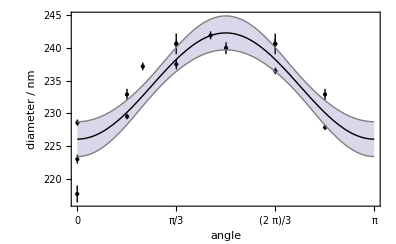

```mathematica
allr=order1r~Join~order2r~Join~order3r~Join~order1sr~Join~order2sr~Join~order21sr;
{0.5*#[[1]]+0.5*#[[2]],0.5*(#[[2]]-#[[1]])}&/@((fit=NonlinearModelFit[{#[[1]],#[[2]]}&/@allr,a Sin[x]^2+b Cos[x]^2,{a,b},x,
ConfidenceLevel->.95,
Weights->(1/#[[3]]&/@allr)
])//#["ParameterConfidenceIntervals"]&)
Show[
ErrorListPlot[allr,PlotRange->All,PlotStyle->Black],
Plot[{Normal@fit,fit["MeanPredictionBands",ConfidenceLevel->.95]},{x,0,Pi},
PlotStyle->{Black,Gray},Filling->{2->{1}}
],Frame->True,FrameTicks->{{Automatic,None},{{0,Pi/6,Pi/3,Pi/2,2Pi/3,5Pi/6,Pi},None}},FrameLabel->{"angle","diameter / nm"}
]
```

```mathematica
direct={{357,9}/3, {382,13}/3,{372,7}/3,{491,9}/4,{371,8}/3}*2//N
```

{{238.,6.},{254.667,8.66667},{248.,4.66667},{245.5,4.5},{247.333,5.33333}}

```mathematica
StandardDeviation[direct[[1;;,1]]]
```

5.97262

```mathematica
weightedMean[direct]
```

{246.258,1.10368}

```mathematica
weightedMean[{{246.258,6.07374},{242.27,2.59372}}]
```

{243.463,1.81755}

```mathematica
(#1/#2)&~applyWithError~{{242.27033758153158,2.593715191644975},{226.05791489631457,2.6565143684023838}}
```

{1.07172,0.017037}